```mathematica
NotebookEvaluate[FileNameJoin[{NotebookDirectory[],"vel_implicit.nb"}],EvaluationElements->"InitializationCell"]
```

#### defVel (parametric)

```mathematica
defVel[F_Symbol,def_List/;(Length[def]==2)]:=Module[{},
(*Off/@{Part::partd,Eliminate::ifun,Solve::ratnz};*)
(* def given is parameterization of bdry(F) in rectangular coordinates *)
Subscript[F, bdryParam]=def;
(* the projective 'dual curve' corresponds to the polar bdry in ℝ^2 (easy check) *)
(F^°)_bdryParam=-Simplify@{
D[(def⟦2⟧), t]/(def⟦2⟧*D[(def⟦1⟧), t]-def⟦1⟧*D[(def⟦2⟧), t]),D[(def⟦1⟧), t]/(def⟦1⟧*D[(def⟦2⟧), t]-def⟦2⟧*D[(def⟦1⟧), t])};


(* derive implicit definition *)
Subscript[F, bdryCnds]=FullSimplify@Eliminate[Subscript[F, bdryParam][[1]]==x&&Subscript[F, bdryParam][[2]]==y,t];
defVel[F,Subscript[F, bdryCnds],"DeriveParametricEquation"->False]
(*On/@{Part::partd,Eliminate::ifun,Solve::ratnz};*)
]
```

#### Ex. 1: Difficult Velocity

```mathematica
(* hard for non-π/4 rotations *)
Clear[t]
First@Timing@Quiet@defVel[F1,ℛ[π/6].({Cos[t],4Sin[t]})]
```

62.9375

```mathematica
Subscript[F1, bdryCnds]
```

2 x+4 Sin[1]==√3 Cos[1]&&2 y==Cos[1]+4 √3 Sin[1]

```mathematica
FullSimplify@∇_{x,y} Subscript[γ, F1][{x,y}]
```

{Piecewise[{{-2., 0.5 y≥1. x&&1. x+0.5 y≤0}, {0.666667, x>0&&1. x+1.5 y≥0&&1. x≥1.5 y}, {0, True}}],Piecewise[{{-1., 0.5 y<1. x&&1. x+1.5 y<0}, {1., 1. x+0.5 y>0&&1. x<1.5 y}, {0, True}}]}

```mathematica
Subscript[γ, F1][{x,y}]
```

Max[-(√((675 x^2+570 √3 x y+361 y^2)/(49 x^2+30 √3 x y+19 y^2)) (49 √3 x^2+90 x y+19 √3 y^2))/(8 (45 x+19 √3 y)),(√((675 x^2+570 √3 x y+361 y^2)/(49 x^2+30 √3 x y+19 y^2)) (49 √3 x^2+90 x y+19 √3 y^2))/(8 (45 x+19 √3 y))]

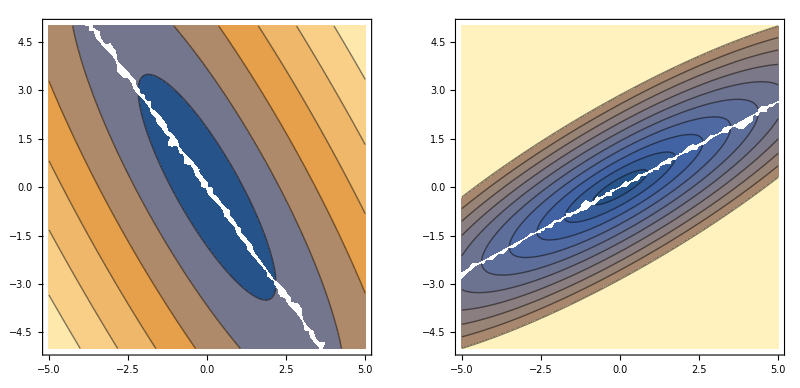

```mathematica
GraphicsRow[Show[{
ContourPlot[#[{x,y}],{x,-5,5},{y,-5,5},Contours->Range[10]],
StreamPlot[Evaluate[∇_{x,y} #[{x,y}]],{x,-5,5},{y,-5,5}]
}]&/@{Subscript[γ, F1],γ_(F1^°)}]
```

#### Ex. 2: Shifted & Rotated Ellipse

```mathematica
First@Timing@Quiet@defVel[F0,1.5{Cos[t],Sin[t]}]
First@Timing@Quiet@defVel[F1,ℛ[π/4].({Cos[t],4Sin[t]}+{1/2,1/10})]
```

0.8125

5.57813

```mathematica
Subscript[γ, F1][{x,y}]
```

(5 √2 (-79 x-81 y+8 √(416 x^2+762 x y+421 y^2)))/1199

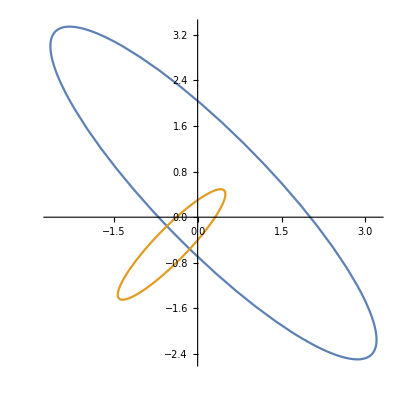

```mathematica
ParametricPlot[{Subscript[F1, bdryParam],(F1^°)_bdryParam},{t,-π,π}]
```

```mathematica
γ_(F1^°)[{x,y}]==1
FullSimplify@Eliminate[Subscript[(F1^°), bdryParam][[1]]==x&&Subscript[(F1^°), bdryParam][[2]]==y,t]
```

(2 x+3 y+5 √(17 x^2-30 x y+17 y^2))/(5 √2)==1

Eliminate::ifun: Inverse functions are being used by Eliminate, so some solutions may not be found; use Reduce for complete solution information.

x (20 √2+421 x-762 y)+30 √2 y+416 y^2==50

```mathematica
Subscript[F1, bdryCnds]
```

10 x (-79 √2+85 x+150 y)==1199+810 √2 y-850 y^2

```mathematica
Subscript[γ, F1][{x,y}]==1
```

(5 √2 (-79 x-81 y+8 √(416 x^2+762 x y+421 y^2)))/1199==1

```mathematica
Solve[Subscript[γ, F1][{x,y}]==1/.{y->0},x]
```

{{x→1/170 (79 √2-64 √13)},{x→1/170 (79 √2+64 √13)}}

```mathematica
GraphicsRow[Show[{
ContourPlot[#[{x,y}],{x,-5,5},{y,-5,5},Contours->Range[10],PlotTheme->"Monochrome"],
StreamPlot[Evaluate[∇_{x,y} #[{x,y}]],{x,-5,5},{y,-5,5},StreamScale->None,StreamStyle->Thick]
}]&/@{Subscript[γ, F1],γ_(F1^°)}]
```

-Graphics-

```mathematica
x0={0,-1};y0={2,0.};T=4;

t00=Subscript[γ, F0][y0-x0]
v0=(y0-x0)/t00
(* Choose ζ0 ∈ Subscript[N, F0](v0) *)
ζ0=Subscript[𝒩̂, F0][v0](* normal cone points *)
ζ2s=Subscript[RefractedNormals, F1][ζ0]
(𝒩̂)_(F1^°)/@ζ2s
v2s=discretize/@Select[(𝒩̂)_(F1^°)/@ζ2s,NonNegative@Last@#&]
```

1.49071

{1.34164,0.67082}

{0.596285,0.298142}

{{0.596285,Undefined},{0.596285,Undefined}}

{{Undefined,Undefined},{Undefined,Undefined}}

{}

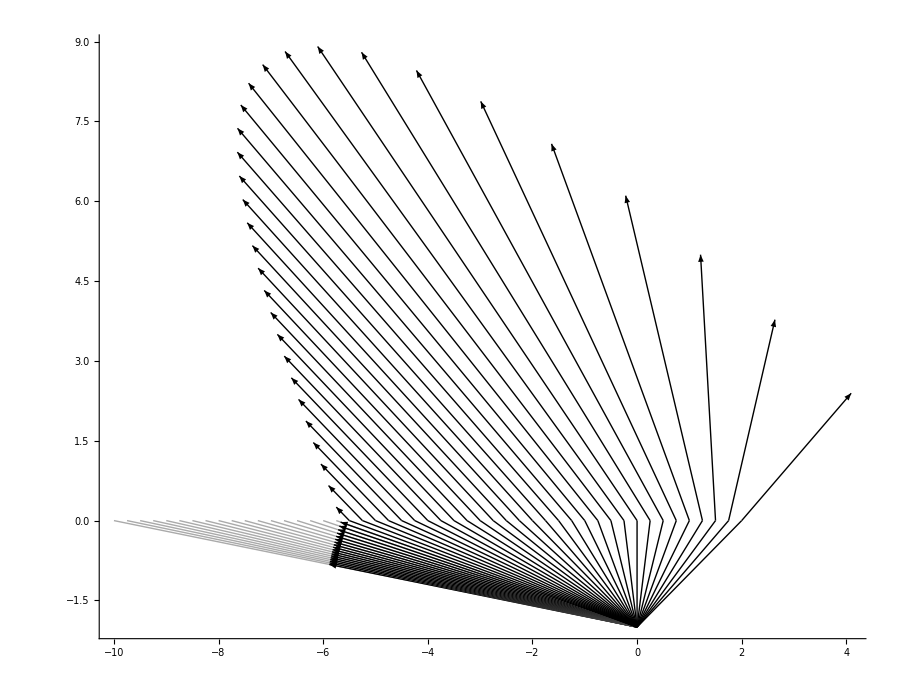

```mathematica
Show[Graphics[{
Arrowheads[Small],
Table[
Module[{x0={0.,-2},T=4,t,y0,v0,ζ0,ζ2s,v2s},
y0={t0,0};
t=Subscript[γ, F0][y0-x0];
v0=(y0-x0)/t;
(* Choose ζ0 ∈ Subscript[N, F0](v0) *)
ζ0=Subscript[𝒩̂, F0][v0](* properly scaled normal cone points *);
(* calculate refracted angles with optimality conditions *)
ζ2s=Subscript[RefractedNormals, F1][ζ0];
v2s=discretize/@Select[(𝒩̂)_(F1^°)/@ζ2s,NonNegative@Last@#&];


If[T>Subscript[γ, F0][y0-x0],
{Black,Line[{x0,y0}],Arrow[{y0,(y0+(T-Subscript[γ, F0][y0-x0])#)}]},
{Lighter@Gray,Line[{x0,y0}],Black,Arrow[{x0,x0+T v0}]}
]&/@v2s

],
{t0,-10,10,0.25}
]},Axes->True]]
```

```mathematica
Select[x/.Solve[Subscript[F1, bdryCnds]/.y->0,{x}],(#>0)&]
```

{1/170 (79 √2+64 √13)}

```mathematica
ListAnimate@Table[
Show[Graphics[{
Arrowheads[Small],
Table[
Module[{x0={0.,-2},t,y0,v0,ζ0,ζ2s,v2s},
y0={t0,0};
t=Subscript[γ, F0][y0-x0];
v0=(y0-x0)/t;
(* Choose ζ0 ∈ Subscript[N, F0](v0) *)
ζ0=Subscript[𝒩̂, F0][v0](* properly scaled normal cone points *);
(* calculate refracted angles with optimality conditions *)
ζ2s=Subscript[RefractedNormals, F1][ζ0];
v2s=discretize/@Select[(𝒩̂)_(F1^°)/@ζ2s,NonNegative@Last@#&];


If[T>Subscript[γ, F0][y0-x0],
{Black,Line[{x0,y0}],Arrow[{y0,(y0+(T-Subscript[γ, F0][y0-x0])#)}]},
{Lighter@Gray,Line[{x0,y0}],Black,Arrow[{x0,x0+T v0}]}
]&/@v2s

],
{t0,-10,10,0.25}
]},Axes->True],ImageSize->Large],
{T,0,4,0.25}]
```